```mathematica
area = 4*π*0.25^2
vol = 4/3 * π (0.25)^3
sphericity = π^(1/3)*(6*vol)^(2/3)/area
```

0.785398

0.0654498

1.

```mathematica
pts = RandomReal[{-1,1},{30,3}];
```

```mathematica
pts = RandomReal[{-1,1},{100,3}];
Min[%]
First@Flatten@Position[pts,%]
Graphics3D[{Point[pts], Red,PointSize[0.05], Point[pts⟦%⟧]},Axes->True]
```

-0.997743

22

-Graphics3D-

```mathematica
First@Flatten@Position[pts,Min[pts]]
```

7

```mathematica
HighlightMesh[DelaunayMesh[RandomReal[{-1,1},{5,1}]],Style[0,Black]]
```

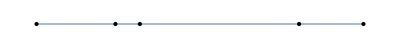

```mathematica
4*π//N
4/3 * π //N
 π^(1/3)*(6*%)^(2/3)/%%//N
```

12.5664

4.18879

1.